```mathematica
Integrate[(1/r)ⅇ^(-2*π*ⅈ*k*r*Cos[θ])*r^(2)*Sin[θ],{ϕ,0,2π}]
```

2 ⅇ^(-2 ⅈ k π r Cos[θ]) π r Sin[θ]

```mathematica
Integrate[%,{θ,0,π}]
```

(2 Sin[2 k π r])/k

```mathematica
Integrate[%,{r,-Infinity,Infinity}]
```

Integrate::idiv: Integral of (2 Sin[2 k π r])/k does not converge on {-∞,∞}.

∫_(-∞)^∞ (2 Sin[2 k π r])/k ⅆr

```mathematica
Integrate[((2π^(2))/(2π)^(3))(1/(k))ⅇ^(-k^(2)/M^(2))ⅇ^(-2*π*ⅈ*k*r*Cos[θ])*k^(2)*Sin[θ],{ϕ,0,2π}]
```

1/2 ⅇ^(-k^2/M^2-2 ⅈ k π r Cos[θ]) k Sin[θ]

```mathematica
Integrate[%,{θ,0,π}]
```

(ⅇ^(-k^2/M^2) Sin[2 k π r])/(2 π r)

```mathematica
Integrate[%,{k,0,Infinity}]
```

ConditionalExpression[(M DawsonF[M π r])/(2 π r),Re[M^2]>0]

```mathematica
Integrate[Sin[θ]*ⅇ^(-ⅈ*k*r*Cos[θ])ⅇ^(-k^(2)/M^(2)),{ϕ,0,2π}]
```

2 ⅇ^(-k^2/M^2-ⅈ k r Cos[θ]) π Sin[θ]

```mathematica
Integrate[%,{θ,0,π}]
```

(4 ⅇ^(-k^2/M^2) π Sin[k r])/(k r)

```mathematica
Integrate[%,{k,0,Infinity}]
```

ConditionalExpression[(2 √(1/M^2) M π^2 Erf[(M r)/2])/r,Re[M^2]>0]

```mathematica
Integrate[G*Q^(2)/(r^(4)),r]
```

```mathematica
Integrate[-(G Q^2)/(3 r^3)+Subscript[C, 1],r]
```

(G Q^2)/(6 r^2)+r C_1

```mathematica
D[(G*Q^(2))/(r^(2))+(G*M)/r,{r,2}]
```

(6 G Q^2)/r^4+(2 G M)/r^3

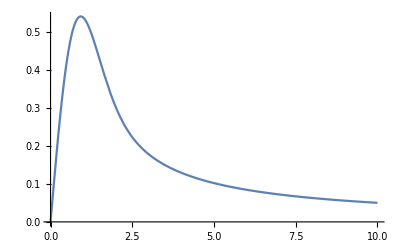

```mathematica
Plot[DawsonF[x],{x,0,10}]
```

```mathematica
Limit[DawsonF[x],x-> Infinity]
```

0

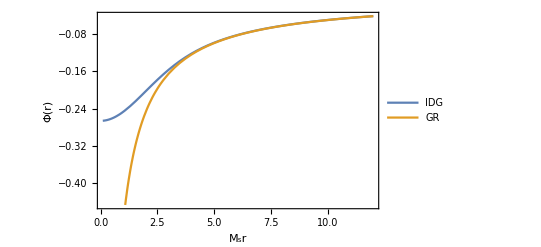

```mathematica
Plot[{-((1*1)/(r/0.5))*Erf[((0.5)(r/0.5)/2)]+((1*(0.5)^(2)*(0.5))/(2*(r/0.5)))DawsonF[((0.5*(r/0.5))/2)],-((1*1)/(r/0.5))+((1*(0.5)^(2)*(0.5))/(2*(r/0.5)^(2)))},{r,0.1,12},
PlotLegends->{"IDG","GR"},FrameLabel->{"M_sr","Φ(r)"},Frame-> True]
```

```mathematica
Φ(r)
```

```mathematica
D[-((G*m)/(r))*Erf[((Subscript[M, s])(r)/2)]+((G*(Q)^(2)*(Subscript[M, s]))/(2*(r)))DawsonF[((Subscript[M, s]*(r))/2)],r]/. {m->1,G-> 1,Q-> 1.6,Subscript[M, s]-> 0.5}
```

-(0.282095 ⅇ^(-0.0625 r^2))/r-(0.64 DawsonF[0.25 r])/r^2+(0.16 (1-0.5 r DawsonF[0.25 r]))/r+Erf[0.25 r]/r^2

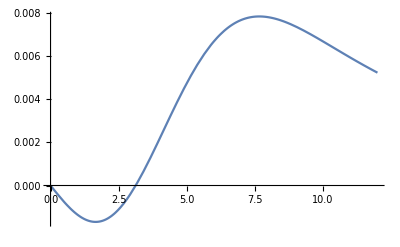

```mathematica
Plot[%,{r,0,12}]
```

```mathematica
2/(0.5)
```

4.

```mathematica
N[Sqrt[2]]
```

1.41421

```mathematica
-((G*m)/(r))*Erf[((Subscript[M, s])(r)/2)]+((G*(Q)^(2)*(Subscript[M, s]))/(2*(r)))DawsonF[((Subscript[M, s]*(r))/2)]/. {m->1,G-> 1,Q-> 1.6,Subscript[M, s]-> 0.5}
```

(0.64 DawsonF[0.25 r])/r-Erf[0.25 r]/r

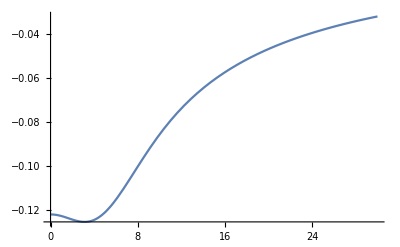

```mathematica
Plot[(0.6400000000000001 DawsonF[0.25 r])/r-Erf[0.25 r]/r,{r,0,30}]
```

```mathematica
Limit[1/2 (-(4 m Erf[(r Subscript[M, s])/2])/r^3+(4 ((ⅇ^(-1/4 r^2 Subscript[M, s]^2) m r)/(√π)+50 DawsonF[(r Subscript[M, s])/2]) Subscript[M, s])/r^3-(100 Subscript[M, s]^2)/r^2+((ⅇ^(-1/4 r^2 Subscript[M, s]^2) m)/(√π)+(50 DawsonF[(r Subscript[M, s])/2])/r) Subscript[M, s]^3-25 Subscript[M, s]^4+25 r DawsonF[(r Subscript[M, s])/2] Subscript[M, s]^5) G,r-> 0]
```

```mathematica
(G Subscript[M, s]^3 (m))/(6 √π)
```

```mathematica
Limit[(ⅇ^(-1/4 M^2 r^2) m (4 M r+M^3 r^3-4 ⅇ^((M^2 r^2)/4) √π Erf[(M r)/2]) G)/(2 √π r^3),r->0]
```

(G m M^3)/(6 √π)

```mathematica
(*IDG*)
```

```mathematica
1/48 (-(96 m Erf[(r Subscript[M, s])/2])/r^3+(((96 ⅇ^(-1/4 r^2 Subscript[M, s]^2) m r)/(√π)+36 Q^2 DawsonF[(r Subscript[M, s])/2]) Subscript[M, s])/r^3-(18 Q^2 Subscript[M, s]^2)/r^2+((16 ⅇ^(-1/4 r^2 Subscript[M, s]^2) m)/(√π)+(12 Q^2 DawsonF[(r Subscript[M, s])/2])/r) Subscript[M, s]^3-3 Q^2 Subscript[M, s]^4+3 Q^2 r DawsonF[(r Subscript[M, s])/2] Subscript[M, s]^5) G/. {G-> 1,m->1,Q-> 0.5,Subscript[M, s]-> 0.5, r-> x/(0.5)}
```

1/48 (-0.046875-0.28125/x^2+0.046875 x DawsonF[0.5 x]+(0.0625 (108.324 ⅇ^(-0.25 x^2) x+9. DawsonF[0.5 x]))/x^3+0.125 ((16 ⅇ^(-0.25 x^2))/(√π)+(1.5 DawsonF[0.5 x])/x)-(12. Erf[0.5 x])/x^3)

```mathematica
(*GR*)
```

```mathematica
(2 (Q^2-m r) G)/r^4/. {G-> 1,m->1,Q-> 0.5,Subscript[M, s]-> 0.5, r-> x/(0.5)}
```

(0.125 (0.25-2. x))/x^4

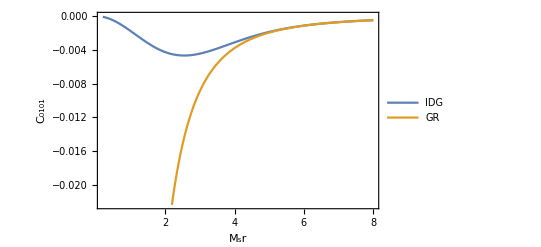

```mathematica
Plot[{1/48 (-0.046875-0.28125/x^2+0.046875 x DawsonF[0.5 x]+(0.0625 (108.32440004116921 ⅇ^(-0.25 x^2) x+9. DawsonF[0.5 x]))/x^3+0.125 ((16 ⅇ^(-0.25 x^2))/(√π)+(1.5 DawsonF[0.5 x])/x)-(12. Erf[0.5 x])/x^3),(0.125 (0.25-2. x))/x^4},{x,0.2,8},PlotLegends->{"IDG","GR"},FrameLabel->{"M_sr","C_0101"},Frame-> True]
```

Kreschmann Scalar
IDG

```mathematica
1/(32 π r^6)ⅇ^(-1/2 r^2 M^2) (1536 ⅇ^(1/2 r^2 M^2) m^2 π Erf[(r M)/2]^2-3072 ⅇ^(1/4 r^2 M^2) m^2 √π r Erf[(r M)/2] M-1152 ⅇ^(1/2 r^2 M^2) m π Q^2 DawsonF[(r M)/2] Erf[(r M)/2] M+1536 m^2 r^2 M^2+1152 ⅇ^(1/4 r^2 M^2) m √π Q^2 r DawsonF[(r M)/2] M^2+240 ⅇ^(1/2 r^2 M^2) π Q^4 DawsonF[(r M)/2]^2 M^2+576 ⅇ^(1/2 r^2 M^2) m π Q^2 r Erf[(r M)/2] M^2-576 ⅇ^(1/4 r^2 M^2) m √π Q^2 r^2 M^3-240 ⅇ^(1/2 r^2 M^2) π Q^4 r DawsonF[(r M)/2] M^3-512 ⅇ^(1/4 r^2 M^2) m^2 √π r^3 Erf[(r M)/2] M^3-384 ⅇ^(1/2 r^2 M^2) m π Q^2 r^2 DawsonF[(r M)/2] Erf[(r M)/2] M^3+60 ⅇ^(1/2 r^2 M^2) π Q^4 r^2 M^4+512 m^2 r^4 M^4+576 ⅇ^(1/4 r^2 M^2) m √π Q^2 r^3 DawsonF[(r M)/2] M^4+160 ⅇ^(1/2 r^2 M^2) π Q^4 r^2 DawsonF[(r M)/2]^2 M^4+96 ⅇ^(1/2 r^2 M^2) m π Q^2 r^3 Erf[(r M)/2] M^4-192 ⅇ^(1/4 r^2 M^2) m √π Q^2 r^4 M^5-120 ⅇ^(1/2 r^2 M^2) π Q^4 r^3 DawsonF[(r M)/2] M^5-96 ⅇ^(1/2 r^2 M^2) m π Q^2 r^4 DawsonF[(r M)/2] Erf[(r M)/2] M^5+20 ⅇ^(1/2 r^2 M^2) π Q^4 r^4 M^6+96 m^2 r^6 M^6+128 ⅇ^(1/4 r^2 M^2) m √π Q^2 r^5 DawsonF[(r M)/2] M^6+72 ⅇ^(1/2 r^2 M^2) π Q^4 r^4 DawsonF[(r M)/2]^2 M^6-32 ⅇ^(1/4 r^2 M^2) m √π Q^2 r^6 M^7-28 ⅇ^(1/2 r^2 M^2) π Q^4 r^5 DawsonF[(r M)/2] M^7+3 ⅇ^(1/2 r^2 M^2) π Q^4 r^6 M^8+32 ⅇ^(1/4 r^2 M^2) m √π Q^2 r^7 DawsonF[(r M)/2] M^8+8 ⅇ^(1/2 r^2 M^2) π Q^4 r^6 DawsonF[(r M)/2]^2 M^8-6 ⅇ^(1/2 r^2 M^2) π Q^4 r^7 DawsonF[(r M)/2] M^9+3 ⅇ^(1/2 r^2 M^2) π Q^4 r^8 DawsonF[(r M)/2]^2 M^10)/. {G-> 1,m->1,Q-> 0.5,M-> 0.5, r-> x/(0.5)}
```

1/x^6 0.000155425 ⅇ^(-0.5 x^2) (1536. x^2-51046.7 ⅇ^(0.25 x^2) x^2+471239. ⅇ^(0.5 x^2) x^2+512. x^4-17015.6 ⅇ^(0.25 x^2) x^4+157080. ⅇ^(0.5 x^2) x^4+96. x^6-2835.93 ⅇ^(0.25 x^2) x^6+23561.9 ⅇ^(0.5 x^2) x^6+102093. ⅇ^(0.25 x^2) x DawsonF[0.5 x]-1.88496×10^6 ⅇ^(0.5 x^2) x DawsonF[0.5 x]+51046.7 ⅇ^(0.25 x^2) x^3 DawsonF[0.5 x]-942478. ⅇ^(0.5 x^2) x^3 DawsonF[0.5 x]+11343.7 ⅇ^(0.25 x^2) x^5 DawsonF[0.5 x]-219911. ⅇ^(0.5 x^2) x^5 DawsonF[0.5 x]+2835.93 ⅇ^(0.25 x^2) x^7 DawsonF[0.5 x]-47123.9 ⅇ^(0.5 x^2) x^7 DawsonF[0.5 x]+1.88496×10^6 ⅇ^(0.5 x^2) DawsonF[0.5 x]^2+1.25664×10^6 ⅇ^(0.5 x^2) x^2 DawsonF[0.5 x]^2+565487. ⅇ^(0.5 x^2) x^4 DawsonF[0.5 x]^2+62831.9 ⅇ^(0.5 x^2) x^6 DawsonF[0.5 x]^2+1.70607×10^7 ⅇ^(0.5 x^2) x^8 DawsonF[0.5 x]^2-5444.98 ⅇ^(0.25 x^2) x Erf[0.5 x]+90477.9 ⅇ^(0.5 x^2) x Erf[0.5 x]-907.496 ⅇ^(0.25 x^2) x^3 Erf[0.5 x]+15079.6 ⅇ^(0.5 x^2) x^3 Erf[0.5 x]-180956. ⅇ^(0.5 x^2) DawsonF[0.5 x] Erf[0.5 x]-60318.6 ⅇ^(0.5 x^2) x^2 DawsonF[0.5 x] Erf[0.5 x]-15079.6 ⅇ^(0.5 x^2) x^4 DawsonF[0.5 x] Erf[0.5 x]+1536 ⅇ^(0.5 x^2) π Erf[0.5 x]^2)

GR

```mathematica
((56 Q^4)/r^8-(96 m Q^2)/r^7+(48 m^2)/r^6) G^2/. {G-> 1,m->1,Q-> 0.5,Subscript[M, s]-> 0.5, r-> x/(0.5)}
```

2187.5/x^8-75./x^7+0.75/x^6

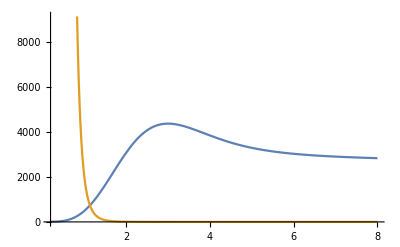

```mathematica
Plot[{1/x^6 0.00015542474911317905 ⅇ^(-0.5 x^2) (1536. x^2-51046.670906078856 ⅇ^(0.25 x^2) x^2+471238.89803846896 ⅇ^(0.5 x^2) x^2+512. x^4-17015.556968692952 ⅇ^(0.25 x^2) x^4+157079.63267948964 ⅇ^(0.5 x^2) x^4+96. x^6-2835.9261614488255 ⅇ^(0.25 x^2) x^6+23561.94490192345 ⅇ^(0.5 x^2) x^6+102093.34181215771 ⅇ^(0.25 x^2) x DawsonF[0.5 x]-1.8849555921538759*^6 ⅇ^(0.5 x^2) x DawsonF[0.5 x]+51046.670906078856 ⅇ^(0.25 x^2) x^3 DawsonF[0.5 x]-942477.7960769379 ⅇ^(0.5 x^2) x^3 DawsonF[0.5 x]+11343.704645795302 ⅇ^(0.25 x^2) x^5 DawsonF[0.5 x]-219911.4857512855 ⅇ^(0.5 x^2) x^5 DawsonF[0.5 x]+2835.9261614488255 ⅇ^(0.25 x^2) x^7 DawsonF[0.5 x]-47123.8898038469 ⅇ^(0.5 x^2) x^7 DawsonF[0.5 x]+1.8849555921538759*^6 ⅇ^(0.5 x^2) DawsonF[0.5 x]^2+1.2566370614359172*^6 ⅇ^(0.5 x^2) x^2 DawsonF[0.5 x]^2+565486.6776461628 ⅇ^(0.5 x^2) x^4 DawsonF[0.5 x]^2+62831.853071795864 ⅇ^(0.5 x^2) x^6 DawsonF[0.5 x]^2+1.7060670482528128*^7 ⅇ^(0.5 x^2) x^8 DawsonF[0.5 x]^2-5444.978229981745 ⅇ^(0.25 x^2) x Erf[0.5 x]+90477.86842338604 ⅇ^(0.5 x^2) x Erf[0.5 x]-907.4963716636241 ⅇ^(0.25 x^2) x^3 Erf[0.5 x]+15079.644737231007 ⅇ^(0.5 x^2) x^3 Erf[0.5 x]-180955.73684677208 ⅇ^(0.5 x^2) DawsonF[0.5 x] Erf[0.5 x]-60318.57894892403 ⅇ^(0.5 x^2) x^2 DawsonF[0.5 x] Erf[0.5 x]-15079.644737231007 ⅇ^(0.5 x^2) x^4 DawsonF[0.5 x] Erf[0.5 x]+1536 ⅇ^(0.5 x^2) π Erf[0.5 x]^2),2187.5/x^8-75./x^7+0.75/x^6},{x,0.2,8}]
```

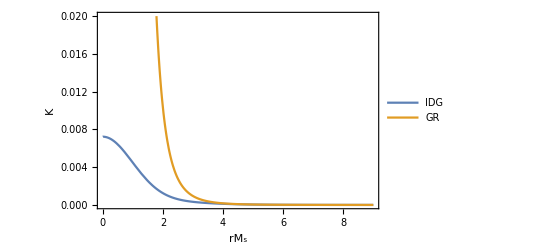

```mathematica
IDGKrech[r_,Q_,M_,m_]:= 1/(32 π r^6)ⅇ^(-1/2 r^2 M^2) (1536 ⅇ^(1/2 r^2 M^2) m^2 π Erf[(r M)/2]^2-3072 ⅇ^(1/4 r^2 M^2) m^2 √π r Erf[(r M)/2] M-1152 ⅇ^(1/2 r^2 M^2) m π Q^2 DawsonF[(r M)/2] Erf[(r M)/2] M+1536 m^2 r^2 M^2+1152 ⅇ^(1/4 r^2 M^2) m √π Q^2 r DawsonF[(r M)/2] M^2+240 ⅇ^(1/2 r^2 M^2) π Q^4 DawsonF[(r M)/2]^2 M^2+576 ⅇ^(1/2 r^2 M^2) m π Q^2 r Erf[(r M)/2] M^2-576 ⅇ^(1/4 r^2 M^2) m √π Q^2 r^2 M^3-240 ⅇ^(1/2 r^2 M^2) π Q^4 r DawsonF[(r M)/2] M^3-512 ⅇ^(1/4 r^2 M^2) m^2 √π r^3 Erf[(r M)/2] M^3-384 ⅇ^(1/2 r^2 M^2) m π Q^2 r^2 DawsonF[(r M)/2] Erf[(r M)/2] M^3+60 ⅇ^(1/2 r^2 M^2) π Q^4 r^2 M^4+512 m^2 r^4 M^4+576 ⅇ^(1/4 r^2 M^2) m √π Q^2 r^3 DawsonF[(r M)/2] M^4+160 ⅇ^(1/2 r^2 M^2) π Q^4 r^2 DawsonF[(r M)/2]^2 M^4+96 ⅇ^(1/2 r^2 M^2) m π Q^2 r^3 Erf[(r M)/2] M^4-192 ⅇ^(1/4 r^2 M^2) m √π Q^2 r^4 M^5-120 ⅇ^(1/2 r^2 M^2) π Q^4 r^3 DawsonF[(r M)/2] M^5-96 ⅇ^(1/2 r^2 M^2) m π Q^2 r^4 DawsonF[(r M)/2] Erf[(r M)/2] M^5+20 ⅇ^(1/2 r^2 M^2) π Q^4 r^4 M^6+96 m^2 r^6 M^6+128 ⅇ^(1/4 r^2 M^2) m √π Q^2 r^5 DawsonF[(r M)/2] M^6+72 ⅇ^(1/2 r^2 M^2) π Q^4 r^4 DawsonF[(r M)/2]^2 M^6-32 ⅇ^(1/4 r^2 M^2) m √π Q^2 r^6 M^7-28 ⅇ^(1/2 r^2 M^2) π Q^4 r^5 DawsonF[(r M)/2] M^7+3 ⅇ^(1/2 r^2 M^2) π Q^4 r^6 M^8+32 ⅇ^(1/4 r^2 M^2) m √π Q^2 r^7 DawsonF[(r M)/2] M^8+8 ⅇ^(1/2 r^2 M^2) π Q^4 r^6 DawsonF[(r M)/2]^2 M^8-6 ⅇ^(1/2 r^2 M^2) π Q^4 r^7 DawsonF[(r M)/2] M^9+3 ⅇ^(1/2 r^2 M^2) π Q^4 r^8 DawsonF[(r M)/2]^2 M^10);
GRKresch[r_,Q_,m_]:= ((56 Q^4)/r^8-(96 m Q^2)/r^7+(48 m^2)/r^6) ;
p1:=Plot[IDGKrech[r/(0.5),0.5,0.5,1],{r,0.002,9},PlotStyle->Orange,PlotLegends->{"BGKM"}];
p2:=Plot[GRKresch[r/(0.5),0.5,1],{r,0.002,9},PlotStyle->Blue,PlotLegends->{"GR"}];
Plot[{IDGKrech[r/(0.5),0.5,0.5,1],GRKresch[r/(0.5),0.5,1]},{r,0.001,9},Frame-> True, FrameLabel-> {"rM_s","K"},PlotLegends->{"IDG","GR"},PlotRange->{0,0.02} ]
```